## matrix-count_tests

Versions of the estimates to test, also validation on test cases that the moments indeed match

### Functions

```mathematica
logBinom[a_,b_]:=LogGamma[a+1]-LogGamma[b+1]-LogGamma[a-b+1]
```

## test_util

### _log_weight

```mathematica
Module[{mat,α},mat={{2,2,3},{2,3,4},{3,4,4}};α=5;Times@@Flatten[Table[Table[Binomial[mat[[i,j]]+α-1,α-1],{j,i+1,3}],{i,1,3}]]*Times@@Table[Binomial[mat[[i,i]]/2+α-1,α-1],{i,1,3}]]//N//Log
```

17.0292

```mathematica
{{2,2,3},{2,3,4},{3,4,4}}
```

```mathematica
17.02920697721357
```

## test_estimate.py

### alpha_symmetric_2

#### diagonal_sum = None

```mathematica
αSymmetric2NoDiag[T_,n_,α_]:=(-((1+n)*(2+n))+T*(2+n*(2+n)))/((-2+n)*(1+n)+T*(2+n))
```

```mathematica
αSymmetric2NoDiag[200,10,1]//N
```

9.75402

```mathematica
αSymmetric2NoDiag[200,10,5]//N
```

41.168

```mathematica
logSymmetric2NoDiag[ks_,α_]:=Module[{T,n,αDM},T=Total[ks];n=Length[ks];αDM=αSymmetric2NoDiag[T,n,α];logBinom[T/2 +α n*(n+1)/2 - 1,α n*(n+1)/2 - 1]-logBinom[T + n αDM - 1, n αDM - 1]  + Total[logBinom[ks+αDM - 1, αDM - 1]]]
```

```mathematica
logSymmetric2NoDiag[{20,11,3},1]//N//Exp
```

38.7629

```mathematica
logSymmetric2NoDiag[{20,11,3},1]//N
```

3.65746

```mathematica
logSymmetric2NoDiag[{20,11,3},5]//N
```

20.3397

#### diagonal_sum

```mathematica
αSymmetric2Diag[T_,Td_,n_,α_]:=-(((-1+n) Td^2 (2+(-1+n) n α)+2 (-1+n) n Td α (2+(-1+n) n α)-(-1+n) T^2 (1+n α) (2+(-1+n) n α)+(-2+n) (T-Td) (1+n α) (T-Td+(-1+n) n α))/(n ((-1+n) Td^2 (2+(-1+n) n α)+2 (-1+n) n Td α (2+(-1+n) n α)-(-1+n) T (1+n α) (2+(-1+n) n α)+(-2+n) (T-Td) (1+n α) (T-Td+(-1+n) n α))))
```

```mathematica
αSymmetric2Diag[200,100,10,1]//N
```

3.6041

```mathematica
αSymmetric2Diag[200,100,10,5]//N
```

13.1526

```mathematica
logSymmetric2Diag[ks_,diagSum_,α_]:=Module[{T,n,αDM},T=Total[ks];n=Length[ks];αDM=αSymmetric2Diag[T,diagSum,n,α]; logBinom[diagSum/2 + α n - 1,α n - 1]+logBinom[(T-diagSum)/2 + α n*(n-1)/2 - 1,α n*(n-1)/2 - 1] -logBinom[T + n αDM - 1, n αDM - 1] + Total[logBinom[ks+αDM - 1, αDM - 1]]]
```

```mathematica
logSymmetric2Diag[{20,11,3},20,1]//N//Exp
```

3.65095

```mathematica
logSymmetric2Diag[{20,11,3},20,1]//N
```

1.29499

```mathematica
logSymmetric2Diag[{20,11,3},20,5]//N
```

18.5925

If the diagonal sum is 0, we simplify since this case is often used in sequential importance sampling

```mathematica
αSymmetric2Diag[T,0,n,α]//Simplify
```

(-((2-3 n+n^2) α)+T (1+(-1+n)^2 α))/(2-2 T-n^2 α+n (-2+T+α))

### alpha_symmetric_3

#### diagonal_sum = None

```mathematica
αSymmetric3NoDiag[T_,n_,α_]:={(T^2 (4+n+(1+n) (4+n (11+4 n)) α+n (1+n)^3 (2+n) α^2)+√((-1+α+n α) (T-(1+n) α) (T+n (1+n) α) (-4-4 n+4 T+3 n T+n (1+n) (n (-1+T)+T) α) (4 (-1+T)+n (-4+5 T+(1+n) (-5+4 T+n (-4+5 T)) α+n (1+n)^2 (-2+n (-1+T)+T) α^2)))+(1+n) T (-4+α (-12+n (-17-11 n-(1+n) (7+n (4+3 n)) α+n (1+n)^3 α^2)))+(1+n)^2 α (8+n (4+α (2+n (7+2 n-(1+n) (4+n) α)))))/(8 (1+n)^2-2 (1+n) (8+5 n) T+2 (4+n (5+2 n)) T^2+n (1+n) (2 n (1+2 n)-3 n (3+n) T+(4+n (3+n)) T^2-2 (1+T)) α+n^2 (1+n)^2 (-3+n (-5+T)+5 T) α^2+2 n^3 (1+n)^3 α^3),(T^2 (4+n+(1+n) (4+n (11+4 n)) α+n (1+n)^3 (2+n) α^2)-√((-1+α+n α) (T-(1+n) α) (T+n (1+n) α) (-4-4 n+4 T+3 n T+n (1+n) (n (-1+T)+T) α) (4 (-1+T)+n (-4+5 T+(1+n) (-5+4 T+n (-4+5 T)) α+n (1+n)^2 (-2+n (-1+T)+T) α^2)))+(1+n) T (-4+α (-12+n (-17-11 n-(1+n) (7+n (4+3 n)) α+n (1+n)^3 α^2)))+(1+n)^2 α (8+n (4+α (2+n (7+2 n-(1+n) (4+n) α)))))/(8 (1+n)^2-2 (1+n) (8+5 n) T+2 (4+n (5+2 n)) T^2+n (1+n) (2 n (1+2 n)-3 n (3+n) T+(4+n (3+n)) T^2-2 (1+T)) α+n^2 (1+n)^2 (-3+n (-5+T)+5 T) α^2+2 n^3 (1+n)^3 α^3)}
```

```mathematica
αSymmetric3NoDiag[200,10,1]//N
```

{13.7998,7.53246}

```mathematica
αSymmetric3NoDiag[200,10,5]//N
```

{63.6326,30.4128}

```mathematica
logSymmetric3NoDiag[ks_,α_]:=Module[{T,n,αP,αM},T=Total[ks];n=Length[ks];αP=αSymmetric3NoDiag[T,n,α][[1]];αM=αSymmetric3NoDiag[T,n,α][[2]];Log[(Exp[logBinom[T/2 + α n*(n+1)/2 - 1,α n*(n+1)/2 - 1]-logBinom[T + n αP - 1, n αP - 1]  + Total[logBinom[ks+αP - 1, αP - 1]]]+Exp[logBinom[T/2 + α n*(n+1)/2 - 1,α n*(n+1)/2 - 1]-logBinom[T + n αM - 1, n αM - 1] + Total[logBinom[ks+αM - 1, αM - 1]]])/2]]
```

```mathematica
logSymmetric3NoDiag[{20,11,3},1]//N
```

3.60119

```mathematica
logSymmetric3NoDiag[{20,11,3},5]//N
```

20.3536

#### diagonal_sum

### alpha_symmetric_block_2

#### diagonal_sum = None

#### diagonal_sum

### alpha_symmetric_block_3

#### diagonal_sum = None

#### diagonal_sum

### alpha_asymmetric_2

### alpha_asymmetric_3

## sample.pyi

### sample_symmetric_matrix

```mathematica
tk= {20,11,3};
```

```mathematica
tT = Total[tk]
tn = Length[tk]
```

34

3

Uniform distribution over all of the matrices with the correct sum:

In order to do this, we need the total number of symmetric matrices to be a reasonable number:

```mathematica
Binomial[tT/2+tn(tn+1)/2-1,tn(tn+1)/2-1]
```

26334

We first generate flattened versions

```mathematica
allFlats=DeleteDuplicates[Flatten[Permutations/@IntegerPartitions[tT/2+tn(tn+1)/2,{tn(tn+1)/2}]-1,1]];
allFlats//Length
allFlats[[30]]
```

26334

{0,0,1,0,0,16}

Which we can then package into symmetric matrices (fix n = 3 for now):

```mathematica
conFlatToMat3[vec_]:={{2*vec[[1]],vec[[2]],vec[[3]]},{vec[[2]],2*vec[[4]],vec[[5]]},{vec[[3]],vec[[5]],2*vec[[6]]}}
```

```mathematica
allMats=conFlatToMat3/@allFlats;
```

```mathematica
allMargins = Total[#]&/@allMats;
```

```mathematica
allMargins[[200]]
```

{16,14,4}

```mathematica
goodPos = Position[allMargins,tk][[;;,1]]
```

{1815,1973,3070,3078,3237,3404,5365,5387,5691,5704,5923,6424,6439,6808,8105,8586,8830,9403,9921,10282,10289,10651,11185,12351,12892,12947,12948,13753,14057,14419,15262,15439,17779,18919}

Compute some correlators

```mathematica
allMats[[goodPos]][[;;,1,2]]*allMats[[goodPos]][[;;,2,3]]//Mean
```

5

```mathematica
allMats[[goodPos]][[;;,1,1]]*allMats[[goodPos]][[;;,1,1]]//Mean//N
```

197.765

```mathematica
allMats[[goodPos]][[;;,3,2]]//Tally
```

{{0,12},{1,12},{3,5},{2,5}}

### sample_asymmetric_matrix

### count_symmetric_matrix

#### Case 1

```mathematica
tk= {20,11,3};
```

```mathematica
tT = Total[tk]
tn = Length[tk]
```

34

3

Uniform distribution over all of the matrices with the correct sum:

In order to do this, we need the total number of symmetric matrices to be a reasonable number:

```mathematica
Binomial[tT/2+tn(tn+1)/2-1,tn(tn+1)/2-1]
```

26334

We first generate flattened versions

```mathematica
allFlats=DeleteDuplicates[Flatten[Permutations/@IntegerPartitions[tT/2+tn(tn+1)/2,{tn(tn+1)/2}]-1,1]];
allFlats//Length
allFlats[[30]]
```

26334

{0,0,1,0,0,16}

Which we can then package into symmetric matrices (fix n = 3 for now):

```mathematica
conFlatToMat3[vec_]:={{2*vec[[1]],vec[[2]],vec[[3]]},{vec[[2]],2*vec[[4]],vec[[5]]},{vec[[3]],vec[[5]],2*vec[[6]]}}
```

```mathematica
allMats=conFlatToMat3/@allFlats;
```

```mathematica
allMargins = Total[#]&/@allMats;
```

```mathematica
allMargins[[200]]
```

{16,14,4}

```mathematica
goodPos = Position[allMargins,tk][[;;,1]]
```

{1815,1973,3070,3078,3237,3404,5365,5387,5691,5704,5923,6424,6439,6808,8105,8586,8830,9403,9921,10282,10289,10651,11185,12351,12892,12947,12948,13753,14057,14419,15262,15439,17779,18919}

Compute some correlators

```mathematica
Zα=Sum[Times@@Flatten[Table[Table[Binomial[mat[[i,j]]+α-1,α-1],{j,i+1,3}],{i,1,3}]]*Times@@Table[Binomial[mat[[i,i]]/2+α-1,α-1],{i,1,3}],{mat,allMats[[goodPos]]}];
```

```mathematica
Zα/.{α->1}
```

34

```mathematica
Zα//Simplify
```

1/4320 α (1080 α^2 (1+α)^2 Binomial[5+α,-1+α]^2+Binomial[5+α,-1+α] (α^2 (2+3 α+α^2)^3 (12+7 α+α^2)+1440 α (1+6 α+5 α^2) Binomial[6+α,-1+α]+720 (2+3 α+7 α^2) Binomial[7+α,-1+α])+2 α (2+3 α+α^2) (α (66+382 α+672 α^2+499 α^3+162 α^4+19 α^5) Binomial[6+α,-1+α]+3 α (39+231 α+347 α^2+189 α^3+34 α^4) Binomial[7+α,-1+α]+3 α (122+453 α+322 α^2+63 α^3) Binomial[8+α,-1+α]+6 (15+122 α+87 α^2+16 α^3) Binomial[9+α,-1+α]+30 (4+15 α+5 α^2) Binomial[10+α,-1+α]))

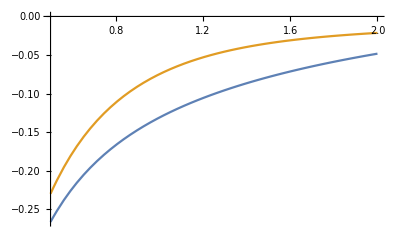

```mathematica
Plot[{Log[Zα]-logSymmetric2NoDiag[{20,11,3},α],Log[Zα]-logSymmetric3NoDiag[{20,11,3},α]},{α,0.5,2}]
```

```mathematica
Log[Zα]/.{α->0.5}
```

-1.45982

```mathematica
Log[Zα]/.{α->5}
```

Log[693809375]

```mathematica
ZαDiag=Sum[Times@@Flatten[Table[Table[Binomial[mat[[i,j]]+α-1,α-1],{j,i+1,3}],{i,1,3}]]*Times@@Table[Binomial[mat[[i,i]]/2+α-1,α-1],{i,1,3}],{mat,Cases[allMats[[goodPos]],x_/;Total[Diagonal[x]]==20]}];
```

```mathematica
ZαDiag/.{α->1}
```

3

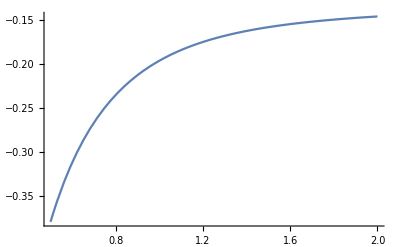

```mathematica
Plot[{Log[ZαDiag]-logSymmetric2Diag[{20,11,3},20,α]},{α,0.5,2}]
```

```mathematica
ZαDiag/.{α->1}//N//Log
```

1.09861

```mathematica
ZαDiag/.{α->5}//N//Log
```

18.4677

1.09861, 18.4677

#### Case 2

```mathematica
tk= {3,3,3,3,2,2};
```

```mathematica
tT = Total[tk]
tn = Length[tk]
```

16

6

Uniform distribution over all of the matrices with the correct sum:

In order to do this, we need the total number of symmetric matrices to be a reasonable number:

```mathematica
Binomial[tT/2+tn(tn+1)/2-1,tn(tn+1)/2-1]
```

3108105

We first generate flattened versions

```mathematica
allFlats=DeleteDuplicates[Flatten[Permutations/@IntegerPartitions[tT/2+tn(tn+1)/2,{tn(tn+1)/2}]-1,1]];
allFlats//Length
```

3108105

Which we can then package into symmetric matrices:

```mathematica
conFlatToMat3[vec_]:={{2*vec[[1]],vec[[2]],vec[[3]]},{vec[[2]],2*vec[[4]],vec[[5]]},{vec[[3]],vec[[5]],2*vec[[6]]}}
```

```mathematica
conFlatToMat[vec_]:=Module[{q,res,t},q =1/2 (-1+√(1+8 Length[vec]));t=1;res=ConstantArray[0,{q,q}];Do[Do[res[[i,j]]+=vec[[t]];res[[j,i]]+=vec[[t]];t+=1,{j,i,q}],{i,1,q}];res]
```

```mathematica
allMats=Monitor[Table[conFlatToMat[allFlats[[ii]]],{ii,1,Length[allFlats]}],{ii}];
```

```mathematica
allMargins = Total[#]&/@allMats;
```

```mathematica
goodPos = Position[allMargins,tk][[;;,1]];
```

```mathematica
Length[goodPos]
```

1828

```mathematica
matsWithMargin=allMats[[goodPos]];
```

Compute some correlators

```mathematica
Zα=Sum[Times@@Flatten[Table[Table[Binomial[mat[[i,j]]+α-1,α-1],{j,i+1,6}],{i,1,6}]]*Times@@Table[Binomial[mat[[i,i]]/2+α-1,α-1],{i,1,6}],{mat,matsWithMargin}];
```

```mathematica
Zα/.{α->1}
```

1828

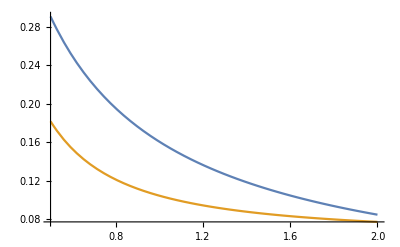

```mathematica
Plot[{Log[Zα]-logSymmetric2NoDiag[tk,α],Log[Zα]-logSymmetric3NoDiag[tk,α]},{α,0.5,2}]
```

```mathematica
Log[Zα]/.{α->1}//N
```

7.51098

```mathematica
Log[Zα]/.{α->5}//N
```

19.8828

```mathematica
diagonalSum=10;
```

```mathematica
matsWithMarginDiag = Cases[matsWithMargin,x_/;Total[Diagonal[x]]==diagonalSum];
```

```mathematica
ZαDiag=Sum[Times@@Flatten[Table[Table[Binomial[mat[[i,j]]+α-1,α-1],{j,i+1,6}],{i,1,6}]]*Times@@Table[Binomial[mat[[i,i]]/2+α-1,α-1],{i,1,6}],{mat,matsWithMarginDiag}];
```

```mathematica
ZαDiag/.{α->1}
```

16

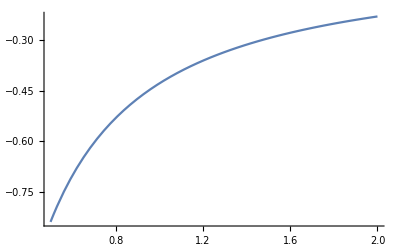

```mathematica
Plot[{Log[ZαDiag]-logSymmetric2Diag[tk,diagonalSum,α]},{α,0.5,2}]
```

```mathematica
ZαDiag/.{α->1}//N//Log
```

2.77259

```mathematica
ZαDiag/.{α->5}//N//Log
```

15.6481

2.77259, 15.6481

### count_asymmetric_matrix

## Moment matching validation

### alpha_symmetric_2

#### diagonal_sum = None

```mathematica
αSymmetric2NoDiag[T_,n_,α_]:= (T+(1+n) (-2+n (-1+T)+T) α)/(2 (-1+T)+n (-2+T+α+n α))
```

```mathematica
αSymmetric2NoDiag[200,10,1]//N
```

9.75402

```mathematica
αSymmetric2NoDiag[200,10,5]//N
```

41.168

#### diagonal_sum

```mathematica
αSymmetric2Diag[T_,Td_,n_,α_]:=-(((-1+n) Td^2 (2+(-1+n) n α)+2 (-1+n) n Td α (2+(-1+n) n α)-(-1+n) T^2 (1+n α) (2+(-1+n) n α)+(-2+n) (T-Td) (1+n α) (T-Td+(-1+n) n α))/(n ((-1+n) Td^2 (2+(-1+n) n α)+2 (-1+n) n Td α (2+(-1+n) n α)-(-1+n) T (1+n α) (2+(-1+n) n α)+(-2+n) (T-Td) (1+n α) (T-Td+(-1+n) n α))))
```

```mathematica
αSymmetric2Diag[200,100,10,1]//N
```

3.6041

```mathematica
αSymmetric2Diag[200,100,10,5]//N
```

13.1526

### alpha_symmetric_3

#### diagonal_sum = None

```mathematica
αSymmetric3NoDiag[T_,n_,α_]:={(T^2 (4+n+(1+n) (4+n (11+4 n)) α+n (1+n)^3 (2+n) α^2)+√((-1+α+n α) (T-(1+n) α) (T+n (1+n) α) (-4-4 n+4 T+3 n T+n (1+n) (n (-1+T)+T) α) (4 (-1+T)+n (-4+5 T+(1+n) (-5+4 T+n (-4+5 T)) α+n (1+n)^2 (-2+n (-1+T)+T) α^2)))+(1+n) T (-4+α (-12+n (-17-11 n-(1+n) (7+n (4+3 n)) α+n (1+n)^3 α^2)))+(1+n)^2 α (8+n (4+α (2+n (7+2 n-(1+n) (4+n) α)))))/(8 (1+n)^2-2 (1+n) (8+5 n) T+2 (4+n (5+2 n)) T^2+n (1+n) (2 n (1+2 n)-3 n (3+n) T+(4+n (3+n)) T^2-2 (1+T)) α+n^2 (1+n)^2 (-3+n (-5+T)+5 T) α^2+2 n^3 (1+n)^3 α^3),(T^2 (4+n+(1+n) (4+n (11+4 n)) α+n (1+n)^3 (2+n) α^2)-√((-1+α+n α) (T-(1+n) α) (T+n (1+n) α) (-4-4 n+4 T+3 n T+n (1+n) (n (-1+T)+T) α) (4 (-1+T)+n (-4+5 T+(1+n) (-5+4 T+n (-4+5 T)) α+n (1+n)^2 (-2+n (-1+T)+T) α^2)))+(1+n) T (-4+α (-12+n (-17-11 n-(1+n) (7+n (4+3 n)) α+n (1+n)^3 α^2)))+(1+n)^2 α (8+n (4+α (2+n (7+2 n-(1+n) (4+n) α)))))/(8 (1+n)^2-2 (1+n) (8+5 n) T+2 (4+n (5+2 n)) T^2+n (1+n) (2 n (1+2 n)-3 n (3+n) T+(4+n (3+n)) T^2-2 (1+T)) α+n^2 (1+n)^2 (-3+n (-5+T)+5 T) α^2+2 n^3 (1+n)^3 α^3)}
```

```mathematica
αSymmetric3NoDiag[200,10,1]//N
```

{13.7998,7.53246}

```mathematica
αSymmetric3NoDiag[200,10,5]//N
```

{63.6326,30.4128}

#### diagonal_sum

### alpha_symmetric_block_2

#### diagonal_sum = None

#### diagonal_sum

### alpha_symmetric_block_3

#### diagonal_sum = None

#### diagonal_sum

### alpha_asymmetric_2

#### diagonal_sum = None

#### diagonal_sum

### alpha_asymmetric_3

#### diagonal_sum = None

#### diagonal_sum

## Workspace

### alpha_symmetric_2

#### diagonal_sum = None

Convert to the c++ format

```mathematica
αSymmetric2NoDiag[2 m,n,α]
```

(2 m+(1+n) (-2+2 m+(-1+2 m) n) α)/(2 (-1+2 m)+n (-2+2 m+α+n α))

2nd central moments of the Dirichlet-Multinomial distribution with total t and length n, we want n → n(n+1)/2 here:

-Graphics-

```mathematica
secondCentralMoment = t/n(n α + t)/(n α + 1)(d - n^(-1));
```

In order to compute the covariances of the degrees this is going to be sum over a variety of contirbutions. We can split into two cases:

i = j:

```mathematica
1+2*(n - 1)+(n-1) + (n-1)(n-2)//Simplify
```

n^2

```mathematica
4*1*(secondCentralMoment/.{t->T/2,n->n(n+1)/2,d->1}) +2*2*(n - 1)*(secondCentralMoment/.{t->T/2,n->n(n+1)/2,d->0})+(n-1)*(secondCentralMoment/.{t->T/2,n->n(n+1)/2,d->1}) + (n-1)(n-2)*(secondCentralMoment/.{t->T/2,n->n(n+1)/2,d->0})//Simplify
```

((-2+n+n^2) T (T+n (1+n) α))/(n^2 (1+n) (2+n α+n^2 α))

```mathematica
(secondCentralMoment/.{d->1}/.{t->T,n->n,α->αM}/.{αM->αSymmetric2NoDiag[T,n,1]}//FullSimplify)==(((-2+n+n^2) T (T+n (1+n) α))/(n^2 (1+n) (2+n α+n^2 α))/.{α->1})
```

((-1+n) (2+n) T (n+n^2+T))/(n^2 (1+n) (2+n+n^2))==((-2+n+n^2) T (n (1+n)+T))/(n^2 (1+n) (2+n+n^2))

```mathematica
Solve[(((-2+n+n^2) T (T+n (1+n) α))/(n^2 (1+n) (2+n α+n^2 α))/.{α->1})==secondCentralMoment/.{d->1}/.{t->T,n->n,α->αM},αM]//FullSimplify
```

{{αM→(-n (3+n)+2 (-1+T)+n (2+n) T)/(2 (-1+T)+n (-1+n+T))}}

```mathematica
Solve[((-2+n+n^2) T (T+n (1+n) α))/(n^2 (1+n) (2+n α+n^2 α))==(secondCentralMoment/.{d->1}/.{t->T,n->n,α->αM}),αM]//FullSimplify
```

{{αM→(T+(1+n) (-2+n (-1+T)+T) α)/(2 (-1+T)+n (-2+T+α+n α))}}

i != j:

```mathematica
1 + 1 + 2(n-1) + ((n-1)^2-1)//Simplify
```

n^2

```mathematica
1 *(secondCentralMoment/.{t->T/2,n->n(n+1)/2,d->1})+ 1 *(secondCentralMoment/.{t->T/2,n->n(n+1)/2,d->0})*4+ 2(n-1)*(secondCentralMoment/.{t->T/2,n->n(n+1)/2,d->0})*2 + ((n-1)^2-1)*(secondCentralMoment/.{t->T/2,n->n(n+1)/2,d->0})//Simplify
```

-((2+n) T (T+n (1+n) α))/(n^2 (1+n) (2+n α+n^2 α))

```mathematica
((-2+n+n^2) T (T+n (1+n) α))/(n^2 (1+n) (2+n α+n^2 α))/(-((2+n) T (T+n (1+n) α))/(n^2 (1+n) (2+n α+n^2 α)))//Simplify
```

1-n

```mathematica
αSymmetric2NoDiag[t,n,1]
```

```mathematica
-((2+n) T (T+n (1+n) α))/(n^2 (1+n) (2+n α+n^2 α))/.{α->1}/.{T->34,n->3}
```

-1955/126

#### diagonal_sum

Convert to the c++ format

```mathematica
αSymmetric2Diag[2 m,2m mu, n,α]
```

-((4 m^2 mu^2 (-1+n) (2+(-1+n) n α)+4 m mu (-1+n) n α (2+(-1+n) n α)-4 m^2 (-1+n) (1+n α) (2+(-1+n) n α)+(2 m-2 m mu) (-2+n) (1+n α) (2 m-2 m mu+(-1+n) n α))/(n (4 m^2 mu^2 (-1+n) (2+(-1+n) n α)+4 m mu (-1+n) n α (2+(-1+n) n α)-2 m (-1+n) (1+n α) (2+(-1+n) n α)+(2 m-2 m mu) (-2+n) (1+n α) (2 m-2 m mu+(-1+n) n α))))

11:

```mathematica
1+2*(n - 1)+(n-1) + (n-1)(n-2)//Simplify
```

n^2

```mathematica
4*1*(secondCentralMoment/.{t->Td/2,n->n,d->1}) +2*2*(n - 1)*0+(n-1)*(secondCentralMoment/.{t->To/2,n->n(n-1)/2,d->1}) + (n-1)(n-2)*(secondCentralMoment/.{t->To/2,n->n(n-1)/2,d->0})//Simplify
```

(((-1+n) Td^2)/(1+n α)+(2 (-1+n) n Td α)/(1+n α)+((-2+n) To (To+(-1+n) n α))/(2-n α+n^2 α))/n^2

```mathematica
(((-1+n) Td^2)/(1+n α)+(2 (-1+n) n Td α)/(1+n α)+((-2+n) To (To+(-1+n) n α))/(2-n α+n^2 α))/n^2/.{α->1,n->3,To->14,Td->20}
```

295/9

```mathematica
αMrule=Solve[(((-1+n) Td^2)/(1+n α)+(2 (-1+n) n Td α)/(1+n α)+((-2+n) To (To+(-1+n) n α))/(2-n α+n^2 α))/n^2==(secondCentralMoment/.{d->1}/.{t->T,n->n,α->αM}),αM][[1]]//FullSimplify
```

{αM→-(((-1+n) Td^2 (2+(-1+n) n α)+2 (-1+n) n Td α (2+(-1+n) n α)-(-1+n) T^2 (1+n α) (2+(-1+n) n α)+(-2+n) To (1+n α) (To+(-1+n) n α))/(n ((-1+n) Td^2 (2+(-1+n) n α)+2 (-1+n) n Td α (2+(-1+n) n α)-(-1+n) T (1+n α) (2+(-1+n) n α)+(-2+n) To (1+n α) (To+(-1+n) n α))))}

```mathematica
αM/.αMrule/.{To->T - Td}//Simplify
```

-(((-1+n) Td^2 (2+(-1+n) n α)+2 (-1+n) n Td α (2+(-1+n) n α)-(-1+n) T^2 (1+n α) (2+(-1+n) n α)+(-2+n) (T-Td) (1+n α) (T-Td+(-1+n) n α))/(n ((-1+n) Td^2 (2+(-1+n) n α)+2 (-1+n) n Td α (2+(-1+n) n α)-(-1+n) T (1+n α) (2+(-1+n) n α)+(-2+n) (T-Td) (1+n α) (T-Td+(-1+n) n α))))

22:

### alpha_symmetric_3

third moment of DM:

```mathematica
thirdCentralMoment = t/n(n α + t)(n α + 2 t)/((n α + 1)(n α + 2))(d3 - d2/n + 2/n^2);
```

#### diagonal_sum = None

111:

```mathematica
1+3(n-1)+3(n-1)+3(n-1)(n-2)+(n-1)(n-2)(n-3)+3(n-1)(n-2)+n-1//Simplify
```

n^3

```mathematica
1(thirdCentralMoment /.{d3->1,d2->3}/.{t->T/2,n->n(n+1)/2})*8+3(n-1)(thirdCentralMoment /.{d3->0,d2->1}/.{t->T/2,n->n(n+1)/2})*4+3(n-1)(thirdCentralMoment /.{d3->0,d2->1}/.{t->T/2,n->n(n+1)/2})*2+3(n-1)(n-2)(thirdCentralMoment /.{d3->0,d2->0}/.{t->T/2,n->n(n+1)/2})*2+(n-1)(n-2)(n-3)*(thirdCentralMoment /.{d3->0,d2->0}/.{t->T/2,n->n(n+1)/2})*1+3(n-1)(n-2)*(thirdCentralMoment /.{d3->0,d2->1}/.{t->T/2,n->n(n+1)/2})*1+(n-1)*(thirdCentralMoment /.{d3->1,d2->3}/.{t->T/2,n->n(n+1)/2})*1//Simplify
```

((8-10 n+n^2+n^3) T (2 T^2+3 n (1+n) T α+n^2 (1+n)^2 α^2))/(n^3 (1+n) (2+n α+n^2 α) (4+n α+n^2 α))

```mathematica
((8-10 n+n^2+n^3) T (2 T^2+3 n (1+n) T α+n^2 (1+n)^2 α^2))/(n^3 (1+n) (2+n α+n^2 α) (4+n α+n^2 α))/.{α->1,T->34,n->3}
```

1955/27

```mathematica
1/2((thirdCentralMoment/.{d3->1,d2->3,t->T}/.{α->alphaMinus})+(thirdCentralMoment/.{d3->1,d2->3,t->T}/.{α->alphaPlus}))/.{T->34,n->3}//Simplify
```

1955/27

```mathematica
Solve[{((8-10 n+n^2+n^3) T (2 T^2+3 n (1+n) T α+n^2 (1+n)^2 α^2))/(n^3 (1+n) (2+n α+n^2 α) (4+n α+n^2 α))==1/2((thirdCentralMoment/.{d3->1,d2->3}/.{t->T,n->n,α->αP})+(thirdCentralMoment/.{d3->1,d2->3}/.{t->T,n->n,α->αM})),((-2+n+n^2) T (T+n (1+n) α))/(n^2 (1+n) (2+n α+n^2 α))==1/2((secondCentralMoment/.{d->1}/.{t->T,n->n,α->αP})+(secondCentralMoment/.{d->1}/.{t->T,n->n,α->αM}))},{αP,αM}]//FullSimplify
```

{{αP→(T^2 (4+n+(1+n) (4+n (11+4 n)) α+n (1+n)^3 (2+n) α^2)+√((-1+α+n α) (T-(1+n) α) (T+n (1+n) α) (-4-4 n+4 T+3 n T+n (1+n) (n (-1+T)+T) α) (4 (-1+T)+n (-4+5 T+(1+n) (-5+4 T+n (-4+5 T)) α+n (1+n)^2 (-2+n (-1+T)+T) α^2)))+(1+n) T (-4+α (-12+n (-17-11 n-(1+n) (7+n (4+3 n)) α+n (1+n)^3 α^2)))+(1+n)^2 α (8+n (4+α (2+n (7+2 n-(1+n) (4+n) α)))))/(8 (1+n)^2-2 (1+n) (8+5 n) T+2 (4+n (5+2 n)) T^2+n (1+n) (2 n (1+2 n)-3 n (3+n) T+(4+n (3+n)) T^2-2 (1+T)) α+n^2 (1+n)^2 (-3+n (-5+T)+5 T) α^2+2 n^3 (1+n)^3 α^3),αM→(T^2 (4+n+(1+n) (4+n (11+4 n)) α+n (1+n)^3 (2+n) α^2)-√((-1+α+n α) (T-(1+n) α) (T+n (1+n) α) (-4-4 n+4 T+3 n T+n (1+n) (n (-1+T)+T) α) (4 (-1+T)+n (-4+5 T+(1+n) (-5+4 T+n (-4+5 T)) α+n (1+n)^2 (-2+n (-1+T)+T) α^2)))+(1+n) T (-4+α (-12+n (-17-11 n-(1+n) (7+n (4+3 n)) α+n (1+n)^3 α^2)))+(1+n)^2 α (8+n (4+α (2+n (7+2 n-(1+n) (4+n) α)))))/(8 (1+n)^2-2 (1+n) (8+5 n) T+2 (4+n (5+2 n)) T^2+n (1+n) (2 n (1+2 n)-3 n (3+n) T+(4+n (3+n)) T^2-2 (1+T)) α+n^2 (1+n)^2 (-3+n (-5+T)+5 T) α^2+2 n^3 (1+n)^3 α^3)},{αP→(T^2 (4+n+(1+n) (4+n (11+4 n)) α+n (1+n)^3 (2+n) α^2)-√((-1+α+n α) (T-(1+n) α) (T+n (1+n) α) (-4-4 n+4 T+3 n T+n (1+n) (n (-1+T)+T) α) (4 (-1+T)+n (-4+5 T+(1+n) (-5+4 T+n (-4+5 T)) α+n (1+n)^2 (-2+n (-1+T)+T) α^2)))+(1+n) T (-4+α (-12+n (-17-11 n-(1+n) (7+n (4+3 n)) α+n (1+n)^3 α^2)))+(1+n)^2 α (8+n (4+α (2+n (7+2 n-(1+n) (4+n) α)))))/(8 (1+n)^2-2 (1+n) (8+5 n) T+2 (4+n (5+2 n)) T^2+n (1+n) (2 n (1+2 n)-3 n (3+n) T+(4+n (3+n)) T^2-2 (1+T)) α+n^2 (1+n)^2 (-3+n (-5+T)+5 T) α^2+2 n^3 (1+n)^3 α^3),αM→(T^2 (4+n+(1+n) (4+n (11+4 n)) α+n (1+n)^3 (2+n) α^2)+√((-1+α+n α) (T-(1+n) α) (T+n (1+n) α) (-4-4 n+4 T+3 n T+n (1+n) (n (-1+T)+T) α) (4 (-1+T)+n (-4+5 T+(1+n) (-5+4 T+n (-4+5 T)) α+n (1+n)^2 (-2+n (-1+T)+T) α^2)))+(1+n) T (-4+α (-12+n (-17-11 n-(1+n) (7+n (4+3 n)) α+n (1+n)^3 α^2)))+(1+n)^2 α (8+n (4+α (2+n (7+2 n-(1+n) (4+n) α)))))/(8 (1+n)^2-2 (1+n) (8+5 n) T+2 (4+n (5+2 n)) T^2+n (1+n) (2 n (1+2 n)-3 n (3+n) T+(4+n (3+n)) T^2-2 (1+T)) α+n^2 (1+n)^2 (-3+n (-5+T)+5 T) α^2+2 n^3 (1+n)^3 α^3)}}

```mathematica
(T^2 (4+n+(1+n) (4+n (11+4 n)) α+n (1+n)^3 (2+n) α^2)+√((-1+α+n α) (T-(1+n) α) (T+n (1+n) α) (-4-4 n+4 T+3 n T+n (1+n) (n (-1+T)+T) α) (4 (-1+T)+n (-4+5 T+(1+n) (-5+4 T+n (-4+5 T)) α+n (1+n)^2 (-2+n (-1+T)+T) α^2)))+(1+n) T (-4+α (-12+n (-17-11 n-(1+n) (7+n (4+3 n)) α+n (1+n)^3 α^2)))+(1+n)^2 α (8+n (4+α (2+n (7+2 n-(1+n) (4+n) α)))))/(8 (1+n)^2-2 (1+n) (8+5 n) T+2 (4+n (5+2 n)) T^2+n (1+n) (2 n (1+2 n)-3 n (3+n) T+(4+n (3+n)) T^2-2 (1+T)) α+n^2 (1+n)^2 (-3+n (-5+T)+5 T) α^2+2 n^3 (1+n)^3 α^3)/.{α->1,T->200,n->10}//N
```

13.7998

```mathematica
(T^2 (4+n+(1+n) (4+n (11+4 n)) α+n (1+n)^3 (2+n) α^2)+√((-1+α+n α) (T-(1+n) α) (T+n (1+n) α) (-4-4 n+4 T+3 n T+n (1+n) (n (-1+T)+T) α) (4 (-1+T)+n (-4+5 T+(1+n) (-5+4 T+n (-4+5 T)) α+n (1+n)^2 (-2+n (-1+T)+T) α^2)))+(1+n) T (-4+α (-12+n (-17-11 n-(1+n) (7+n (4+3 n)) α+n (1+n)^3 α^2)))+(1+n)^2 α (8+n (4+α (2+n (7+2 n-(1+n) (4+n) α)))))/(8 (1+n)^2-2 (1+n) (8+5 n) T+2 (4+n (5+2 n)) T^2+n (1+n) (2 n (1+2 n)-3 n (3+n) T+(4+n (3+n)) T^2-2 (1+T)) α+n^2 (1+n)^2 (-3+n (-5+T)+5 T) α^2+2 n^3 (1+n)^3 α^3)/.{Sqrt[a_]->0}//FullSimplify
```

(T^2 (4+n+(1+n) (4+n (11+4 n)) α+n (1+n)^3 (2+n) α^2)+(1+n) T (-4+α (-12+n (-17-11 n-(1+n) (7+n (4+3 n)) α+n (1+n)^3 α^2)))+(1+n)^2 α (8+n (4+α (2+n (7+2 n-(1+n) (4+n) α)))))/(8 (1+n)^2-2 (1+n) (8+5 n) T+2 (4+n (5+2 n)) T^2+n (1+n) (2 n (1+2 n)-3 n (3+n) T+(4+n (3+n)) T^2-2 (1+T)) α+n^2 (1+n)^2 (-3+n (-5+T)+5 T) α^2+2 n^3 (1+n)^3 α^3)

```mathematica
denominator=
```

```mathematica
(T^2 (4+n+(1+n) (4+n (11+4 n)) α+n (1+n)^3 (2+n) α^2)+(1+n) T (-4+α (-12+n (-17-11 n-(1+n) (7+n (4+3 n)) α+n (1+n)^3 α^2)))+(1+n)^2 α (8+n (4+α (2+n (7+2 n-(1+n) (4+n) α)))))/.{T->200,n->10,α->1}
```

6820008328

#### diagonal_sum

111:

```mathematica
1+3(n-1)+3(n-1)+3(n-1)(n-2)+(n-1)(n-2)(n-3)+3(n-1)(n-2)+n-1//Simplify
```

n^3

```mathematica
1(thirdCentralMoment /.{d3->1,d2->3}/.{t->Td/2,n->n})*8+3(n-1)(thirdCentralMoment /.{d3->0,d2->1}/.{t->T/2,n->n(n+1)/2})*0+3(n-1)(thirdCentralMoment /.{d3->0,d2->1}/.{t->T/2,n->n(n+1)/2})*0+3(n-1)(n-2)(thirdCentralMoment /.{d3->0,d2->0}/.{t->T/2,n->n(n+1)/2})*0+(n-1)(n-2)(n-3)*(thirdCentralMoment /.{d3->0,d2->0}/.{t->To/2,n->n(n-1)/2})*1+3(n-1)(n-2)*(thirdCentralMoment /.{d3->0,d2->1}/.{t->To/2,n->n(n-1)/2})*1+(n-1)*(thirdCentralMoment /.{d3->1,d2->3}/.{t->To/2,n->n(n-1)/2})*1//Simplify
```

(8 (-3+n) (-2+n) To (1+n α) (2+n α) (To+(-1+n) n α) (2 To+(-1+n) n α)-6 (-2+n) (-4-n+n^2) To (1+n α) (2+n α) (To+(-1+n) n α) (2 To+(-1+n) n α)+(8+6 n-5 n^2-2 n^3+n^4) To (1+n α) (2+n α) (To+(-1+n) n α) (2 To+(-1+n) n α)+2 (-1+n)^2 (2-3 n+n^2) Td (Td+n α) (Td+2 n α) (2-n α+n^2 α) (4-n α+n^2 α))/(4 (-1+n)^2 n^3 (1+n α) (2+n α) (1+1/2 (-1+n) n α) (2+1/2 (-1+n) n α))

```mathematica
(8 (-3+n) (-2+n) To (1+n α) (2+n α) (To+(-1+n) n α) (2 To+(-1+n) n α)-6 (-2+n) (-4-n+n^2) To (1+n α) (2+n α) (To+(-1+n) n α) (2 To+(-1+n) n α)+(8+6 n-5 n^2-2 n^3+n^4) To (1+n α) (2+n α) (To+(-1+n) n α) (2 To+(-1+n) n α)+2 (-1+n)^2 (2-3 n+n^2) Td (Td+n α) (Td+2 n α) (2-n α+n^2 α) (4-n α+n^2 α))/(4 (-1+n)^2 n^3 (1+n α) (2+n α) (1+1/2 (-1+n) n α) (2+1/2 (-1+n) n α))/.{α->1,n->3,To->14,Td->20}
```

2273/27

```mathematica
Solve[{(8 (-3+n) (-2+n) To (1+n α) (2+n α) (To+(-1+n) n α) (2 To+(-1+n) n α)-6 (-2+n) (-4-n+n^2) To (1+n α) (2+n α) (To+(-1+n) n α) (2 To+(-1+n) n α)+(8+6 n-5 n^2-2 n^3+n^4) To (1+n α) (2+n α) (To+(-1+n) n α) (2 To+(-1+n) n α)+2 (-1+n)^2 (2-3 n+n^2) Td (Td+n α) (Td+2 n α) (2-n α+n^2 α) (4-n α+n^2 α))/(4 (-1+n)^2 n^3 (1+n α) (2+n α) (1+1/2 (-1+n) n α) (2+1/2 (-1+n) n α))==1/2((thirdCentralMoment/.{d3->1,d2->3}/.{t->T,n->n,α->αP})+(thirdCentralMoment/.{d3->1,d2->3}/.{t->T,n->n,α->αM})),(((-1+n) Td^2)/(1+n α)+(2 (-1+n) n Td α)/(1+n α)+((-2+n) To (To+(-1+n) n α))/(2-n α+n^2 α))/n^2==1/2((secondCentralMoment/.{d->1}/.{t->T,n->n,α->αP})+(secondCentralMoment/.{d->1}/.{t->T,n->n,α->αM}))},{αP,αM}]//FullSimplify
```

$Aborted

```mathematica
Solve[{((8 (-3+n) (-2+n) To (1+n α) (2+n α) (To+(-1+n) n α) (2 To+(-1+n) n α)-6 (-2+n) (-4-n+n^2) To (1+n α) (2+n α) (To+(-1+n) n α) (2 To+(-1+n) n α)+(8+6 n-5 n^2-2 n^3+n^4) To (1+n α) (2+n α) (To+(-1+n) n α) (2 To+(-1+n) n α)+2 (-1+n)^2 (2-3 n+n^2) Td (Td+n α) (Td+2 n α) (2-n α+n^2 α) (4-n α+n^2 α))/(4 (-1+n)^2 n^3 (1+n α) (2+n α) (1+1/2 (-1+n) n α) (2+1/2 (-1+n) n α))/.{α->1})==1/2((thirdCentralMoment/.{d3->1,d2->3}/.{t->T,n->n,α->αP})+(thirdCentralMoment/.{d3->1,d2->3}/.{t->T,n->n,α->αM})),((((-1+n) Td^2)/(1+n α)+(2 (-1+n) n Td α)/(1+n α)+((-2+n) To (To+(-1+n) n α))/(2-n α+n^2 α))/n^2/.{α->1})==1/2((secondCentralMoment/.{d->1}/.{t->T,n->n,α->αP})+(secondCentralMoment/.{d->1}/.{t->T,n->n,α->αM}))},{αP,αM}]//FullSimplify
```

$Aborted

### alpha_symmetric_block_2

#### diagonal_sum = None

#### diagonal_sum

### alpha_symmetric_block_3

#### diagonal_sum = None

#### diagonal_sum

### alpha_asymmetric_2

#### diagonal_sum = None

#### diagonal_sum

### alpha_asymmetric_3

#### diagonal_sum = None

#### diagonal_sum